# ChristopherWolfram/ForeignFunctionInterface

Efficiently connect to C-compatible libraries

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ForeignFunctionInterface.nb"DocumentationEnglishGuidesForeignFunctionInterface.nb

"ReferencePages"

"Symbols"

"BufferToList.nb"DocumentationEnglishReferencePagesSymbolsBufferToList.nb

"BufferToNumericArray.nb"DocumentationEnglishReferencePagesSymbolsBufferToNumericArray.nb

"BufferToString.nb"DocumentationEnglishReferencePagesSymbolsBufferToString.nb

"CallForeignFunction.nb"DocumentationEnglishReferencePagesSymbolsCallForeignFunction.nb

"CreateBuffer.nb"DocumentationEnglishReferencePagesSymbolsCreateBuffer.nb

"CreateCallback.nb"DocumentationEnglishReferencePagesSymbolsCreateCallback.nb

"CreateForeignFunction.nb"DocumentationEnglishReferencePagesSymbolsCreateForeignFunction.nb

"CreateManagedExpression.nb"DocumentationEnglishReferencePagesSymbolsCreateManagedExpression.nb

"DeleteBuffer.nb"DocumentationEnglishReferencePagesSymbolsDeleteBuffer.nb

"DeleteCallback.nb"DocumentationEnglishReferencePagesSymbolsDeleteCallback.nb

"DereferenceBuffer.nb"DocumentationEnglishReferencePagesSymbolsDereferenceBuffer.nb

"ForeignFunction.nb"DocumentationEnglishReferencePagesSymbolsForeignFunction.nb

"GetManagedExpression.nb"DocumentationEnglishReferencePagesSymbolsGetManagedExpression.nb

"ListToBuffer.nb"DocumentationEnglishReferencePagesSymbolsListToBuffer.nb

"NumericArrayToBuffer.nb"DocumentationEnglishReferencePagesSymbolsNumericArrayToBuffer.nb

"OpaqueRawPointer.nb"DocumentationEnglishReferencePagesSymbolsOpaqueRawPointer.nb

"PopulateBuffer.nb"DocumentationEnglishReferencePagesSymbolsPopulateBuffer.nb

"StringToBuffer.nb"DocumentationEnglishReferencePagesSymbolsStringToBuffer.nb

"Tutorials"

"CreatingALinkToSQLite.nb"DocumentationEnglishTutorialsCreatingALinkToSQLite.nb

"FFITypes.nb"DocumentationEnglishTutorialsFFITypes.nb

"Kernel"

"Buffer.wl"KernelBuffer.wl

"ExternalLibrary.wl"KernelExternalLibrary.wl

"ForeignFunctionInterface.wl"KernelForeignFunctionInterface.wl

"ForeignFunction.wl"KernelForeignFunction.wl

"LibFFI"

"BaseTypes.wl"KernelLibFFIBaseTypes.wl

"Callback.wl"KernelLibFFICallback.wl

"CallForeignFunction.wl"KernelLibFFICallForeignFunction.wl

"Constants.wl"KernelLibFFIConstants.wl

"CreateForeignFunction.wl"KernelLibFFICreateForeignFunction.wl

"ExpressionConversion.wl"KernelLibFFIExpressionConversion.wl

"FFIType.wl"KernelLibFFIFFIType.wl

"LibFFI.wl"KernelLibFFILibFFI.wl

"RawFunctionLoading.wl"KernelLibFFIRawFunctionLoading.wl

"ManagedExpression.wl"KernelManagedExpression.wl

"Messages.wl"KernelMessages.wl

"OpaqueRawPointer.wl"KernelOpaqueRawPointer.wl

"LibraryResources"

"Linux-x86-64"

"ffiConstants.so"LibraryResourcesLinux-x86-64ffiConstants.so

"ForeignFunctionInterface.so"LibraryResourcesLinux-x86-64ForeignFunctionInterface.so

"libffi.a"LibraryResourcesLinux-x86-64libffi.a

"libffi.la"LibraryResourcesLinux-x86-64libffi.la

"libffi.so"LibraryResourcesLinux-x86-64libffi.so

"libffi.so.8"LibraryResourcesLinux-x86-64libffi.so.8

"libffi.so.8.1.2"LibraryResourcesLinux-x86-64libffi.so.8.1.2

"MacOSX-x86-64"

"ffiConstants.dylib"LibraryResourcesMacOSX-x86-64ffiConstants.dylib

"ForeignFunctionInterface.dylib"LibraryResourcesMacOSX-x86-64ForeignFunctionInterface.dylib

"libffi.8.dylib"LibraryResourcesMacOSX-x86-64libffi.8.dylib

"libffi.a"LibraryResourcesMacOSX-x86-64libffi.a

"libffi.dylib"LibraryResourcesMacOSX-x86-64libffi.dylib

"libffi.la"LibraryResourcesMacOSX-x86-64libffi.la

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

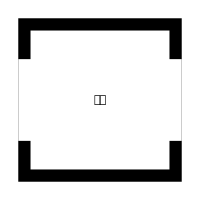

```mathematica
Graphics[{
{Black,Rectangle[{-1,-1},{1,1}],
White,Rectangle[{-0.85,-0.85},{0.85,0.85}],
Rectangle[{-1,-0.5},{1,0.5}]
},
{FontSize->Scaled[0.35],Text["𒅴𒁇"]}
},PlotRange->1,PlotRangePadding->0]
```

### Basic Description

ForeignFunctionInterface makes it possible to efficiently call functions from C-compatible libraries directly from the Wolfram Language, without the need to compile an interface layer.

### Details

This paclet uses libffi to dynamically link to C-compatible libraries at runtime

Though this paclet could be built on all platforms supported by Wolfram Language, it is currently only built for x86 macOS and Linux.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["ChristopherWolfram`ForeignFunctionInterface`"];
```

### Basic Examples

Load a library:

```mathematica
demoLib=LoadExternalLibrary["compilerDemoBase"]
```

ExternalLibrary[…]

Create a ForeignFunction referring to a function from the library:

```mathematica
addone=ForeignFunction[demoLib,"addone",{"CInt"}->"CInt"]
```

ForeignFunction[…]

Call the foreign function:

```mathematica
addone[12]
```

13

### Scope

Loading functions can have some overhead (especially on macOS):

```mathematica
ForeignFunction[demoLib,"addone",{"CInt"}->"CInt"]//RepeatedTiming
```

{3.44522×10^-6,ForeignFunction[…]}

It is more efficient to store ForeignFunction objects if they are used more than once:

```mathematica
addone[12]//RepeatedTiming
```

{7.52631×10^-7,13}

Functions from libraries loaded into the system with LibraryLoad are always in scope:

```mathematica
LibraryLoad["compilerDemoBase"];
```

```mathematica
ForeignFunction["addone",{"CInt"}->"CInt"][12]
```

13

### Applications

Create a foreign function for the RAND_bytes function from OpenSSL:

```mathematica
randBytes=ForeignFunction["RAND_bytes",{"OpaqueRawPointer","CInt"}->"CInt"]
```

ForeignFunction[…]

Create a memory-managed buffer into which the random bytes can be written:

```mathematica
out=CreateManagedExpression[CreateBuffer["UnsignedInteger8",32],DeleteBuffer]
```

DataStructure[ManagedExpression, $Failed]

Generate the random bytes:

```mathematica
randBytes[out,32]
```

1

Read the output:

```mathematica
Normal@BufferToNumericArray[out,"UnsignedInteger8",32]
```

{201,207,150,98,124,252,212,250,118,65,222,78,254,138,173,67,178,70,85,173,68,19,5,85,64,22,48,211,49,165,54,162}

Package into a function:

```mathematica
generateRandomBytes[len_]:=
Module[{out=CreateManagedExpression[CreateBuffer["UnsignedInteger8",len],DeleteBuffer]},
randBytes[out,len];
BufferToNumericArray[out,"UnsignedInteger8",len]
]
```

```mathematica
Normal@generateRandomBytes[128]
```

{227,140,39,227,234,43,239,219,58,124,154,162,138,150,172,58,91,26,135,8,117,3,247,205,239,136,2,157,230,128,62,163,193,8,191,23,25,224,73,1,165,99,215,127,44,106,224,228,164,250,241,84,164,41,71,239,102,132,156,240,165,25,103,67,41,109,80,142,96,211,44,253,96,90,214,241,168,201,26,10,143,246,24,205,235,233,65,119,163,7,96,52,152,136,71,17,194,217,68,236,128,37,157,228,51,104,83,226,73,118,111,190,214,75,208,79,97,165,77,166,231,153,158,196,206,88,180,175}

The foreign function is very efficient:

```mathematica
RepeatedTiming[generateRandomBytes[10000000];]
```

{0.00347429,Null}

```mathematica
RepeatedTiming[RandomInteger[{0,255},10000000];]
```

{0.0359074,Null}

Create a foreign function for the SHA256 function from OpenSSL:

```mathematica
sha256=ForeignFunction["SHA256",{"OpaqueRawPointer","CUnsignedLong","OpaqueRawPointer"}->"OpaqueRawPointer"]
```

ForeignFunction[…]

Create a buffer containing the plaintext to hash:

```mathematica
plaintext="Hello, World!";
plaintextBuffer=CreateManagedExpression[StringToBuffer[plaintext],DeleteBuffer]
```

DataStructure[ManagedExpression, $Failed]

Create a buffer into which to write the hash:

```mathematica
ciphertext=CreateManagedExpression[CreateBuffer["UnsignedInteger8",32],DeleteBuffer]
```

DataStructure[ManagedExpression, $Failed]

Generate inputs and execute the hash:

```mathematica
sha256[plaintextBuffer,StringLength[plaintext],ciphertext]
```

OpaqueRawPointer[…]

Extract the results:

```mathematica
Normal@BufferToNumericArray[ciphertext,"UnsignedInteger8",32]
```

{223,253,96,33,187,43,213,176,175,103,98,144,128,158,195,165,49,145,221,129,199,247,10,75,40,104,138,54,33,130,152,111}

Compare with the built-in function Hash:

```mathematica
Normal@Hash[plaintext,"SHA256","ByteArray"]
```

{223,253,96,33,187,43,213,176,175,103,98,144,128,158,195,165,49,145,221,129,199,247,10,75,40,104,138,54,33,130,152,111}

Package into a function:

```mathematica
generateSHA256[plaintext_]:=
Module[{
plaintextBuffer=CreateManagedExpression[StringToBuffer[plaintext],DeleteBuffer],
ciphertext=CreateManagedExpression[CreateBuffer["UnsignedInteger8",32],DeleteBuffer]
},
sha256[plaintextBuffer,StringLength[plaintext],ciphertext];
BufferToNumericArray[ciphertext,"UnsignedInteger8",32]
]
```

```mathematica
generateSHA256["Hello, World!"]//Normal
```

{223,253,96,33,187,43,213,176,175,103,98,144,128,158,195,165,49,145,221,129,199,247,10,75,40,104,138,54,33,130,152,111}

The packaged function is much faster than the built-in one:

```mathematica
RepeatedTiming@generateSHA256[plaintext]
```

{7.81001×10^-6,NumericArray[…]}

```mathematica
RepeatedTiming@Hash[plaintext,"SHA256","ByteArray"]
```

{0.000142453,ByteArray[…]}

### Properties and Relations

ForeignFunction can create callable links to libraries much faster than custom compiling a link:

```mathematica
demoLib=LoadExternalLibrary["compilerDemoBase"];
```

```mathematica
RepeatedTiming[addone=ForeignFunction[demoLib,"addone",{"CInt"}->"CInt"]]
```

{3.65039×10^-6,ForeignFunction[…]}

```mathematica
RepeatedTiming[addoneCf=FunctionCompile[
LibraryFunctionDeclaration["addone","compilerDemoBase",{"CInt"}->"CInt"],
Function[Typed[x,"CInt"],LibraryFunction["addone"][x]]
]]
```

{0.17542,CompiledCodeFunction[…]}

However, the custom compiled versions usually have slightly less overhead:

```mathematica
RepeatedTiming[addone[10]]
```

{7.74954×10^-7,11}

```mathematica
RepeatedTiming[addoneCf[10]]
```

{1.51246×10^-7,11}

### Possible Issues

## Source & Additional Information

### Creator

Christopher Wolfram

### Source Control Repository

https://github.com/chriswolfram/ForeignFunctionInterface

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

FFI

foreign function interface

library

libraries

dynamic libraries

dynamic library

external libraries

external library

C

linking

link

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

libffi homepage

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

There are some know issues with managed expressions. The design of that system will likely have to change. For example, managed expressions stored in a With are often freed before their bodies can be used:

```mathematica
With[{buf=CreateManagedExpression[foo,Echo["freed"]&]},
EchoLabel["func"][GetManagedExpression[buf]]
]
```

freed

func  foo

foo

This is still a work in progress, and there are a few missing features, though they are all relatively simple to implement. Here are some of them:

Windows support. The current platform list is just those that I can easily build for.

More functions for creating and manipulating buffers / structs.

More natural calling syntax.

Perhaps automatic type conversion (so a string could be passed to an argument with type OpaqueRawPointer, etc.)

The logo for this paclet is Sumerian for "foreign language" (or at least an attempt to mean that).